```mathematica
(*Fixed Points and Chemical Potential*)


(*Noninteracting Bosons*)
Num=100; (*# of atoms*)
gr=40.0(*40.0*);
uf=0.3;
m=1.0;
kr=18.0;
(*Define the constants*)
α[x_,k_]:=(m*k*x)/(2*π^2)-(2*m*x)^(3/2)/(4*π^2)ArcTan[k/(√(2*m*x))];

β[x_]:=(2*m*x)^(3/2)/(128*π)*Num;
γ[x_,k_]:=(m*k*x)/(2*π^2)+x/uf;

κ[x_]:=gr^2/(32*π)*(2*m*x)^(3/2)/x^2;
λ[x_,ν_]:=(ν+x)/(32*π)*(2*m*x)^(3/2)/x;
σ[x_]:=x/gr;

ξsq[x_,k_]:=x^2*((m (-2 k m x+√2 √(m x) (k^2+2 m x) ArcTan[k/(√2 √(m x))]))/(4 π^2 x (k^2+2 m x)));

ζ[x_,ν_,k_]:=λ[x,ν]/(κ[x]*γ[x,k]);
η[x_,ν_,k_]:=ζ[x,ν,k]/(1+ζ[x,ν,k]);
```

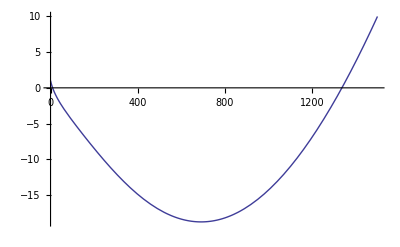

```mathematica
ν=-1300;

Plot[1-(α[e,kr]-η[e,ν,kr]γ[e,kr])/β[e]*(2 σ[e]^2*(1-η[e,ν,kr])^2+ξsq[e,kr]),{e,0,1500}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

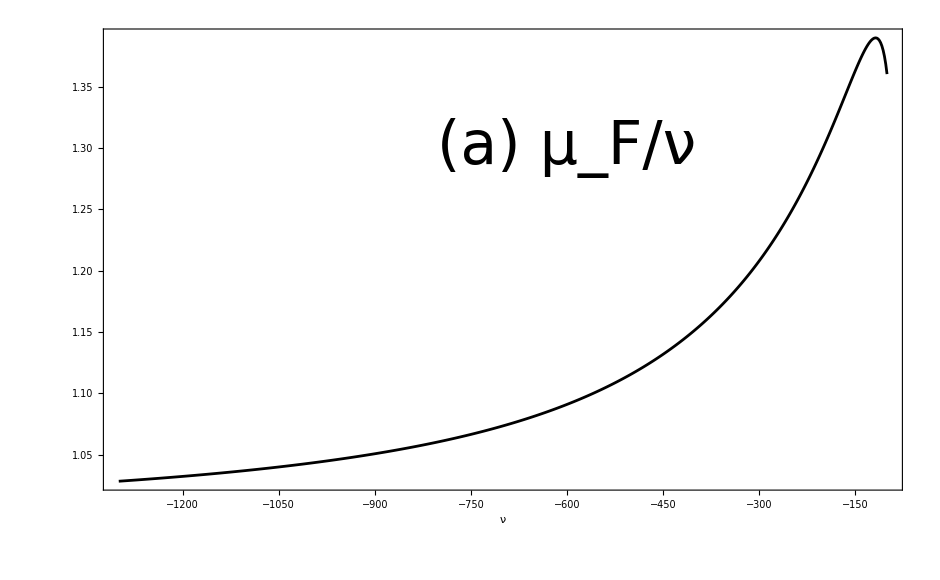

```mathematica
Data1=Table[{ν,1/ν*(-FindRoot[1-(α[e,kr]-η[e,ν,kr]γ[e,kr])/β[e]*(2 σ[e]^2*(1-η[e,ν,kr])^2+ξsq[e,kr]),{e,1301}][[1]][[2]])},{ν,-1300,-100.0,2.0}];
p1=ListPlot[Data1,Joined->True,Axes->False,Frame->True,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2],RGBColor[0,0,0]},FrameTicksStyle->Thick];
p1label=Graphics[Text[Style["(a) μ_F/ν",FontSize->60],{-600,1.3}]];
p100neg=Show[p1,p1label]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

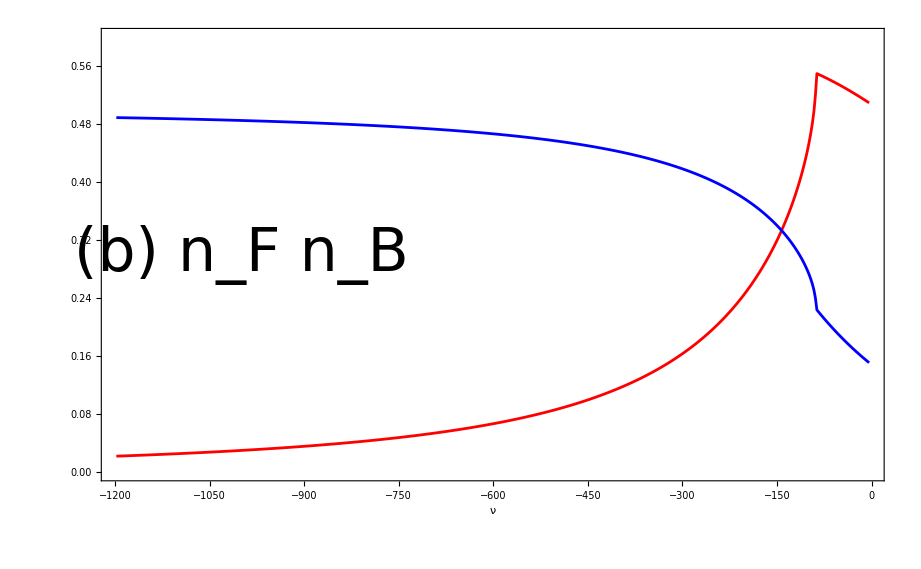

```mathematica
νinit=-1200.0;
νfinal=-5;
νincr=2.3;
Fermi1=Table[ν,{ν,νinit, νfinal,νincr}];
Bose1=Fermi1;
L=Length[Fermi1]+1;
For[i=1,i≤ L-1,i++,
ν=νinit+i*νincr;
e=FindRoot[1-(α[e,kr]-η[e,ν,kr]γ[e,kr])/β[e]*(2 σ[e]^2*(1-η[e,ν,kr])^2+ξsq[e,kr]),{e,1301}][[1]][[2]];
Fermi1[[i]]= {ν,ξsq[e,kr]*(α[e,kr]-η[e,ν,kr]γ[e,kr])/β[e]};
Bose1[[i]]={ν,σ[e]^2*(1-η[e,ν,kr])^2*(α[e,kr]-η[e,ν,kr]γ[e,kr])/β[e]};

];
Fermi1plot=ListPlot[Fermi1,Joined->True,Frame->True,Axes->False,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2],RGBColor[1,0,0]},FrameTicksStyle->Thick];
Fermi1label=Graphics[Text[Style["(b) n_F n_B",FontSize->60],{-1000,0.3}]];
Bose1plot=ListPlot[Bose1,Joined->True,Frame->True,FrameLabel->None,RotateLabel->False,PlotStyle->{AbsoluteThickness[2],RGBColor[0,0,1]}];
n100=Show[Fermi1plot,Bose1plot,Fermi1label,PlotRange->{0,0.6}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

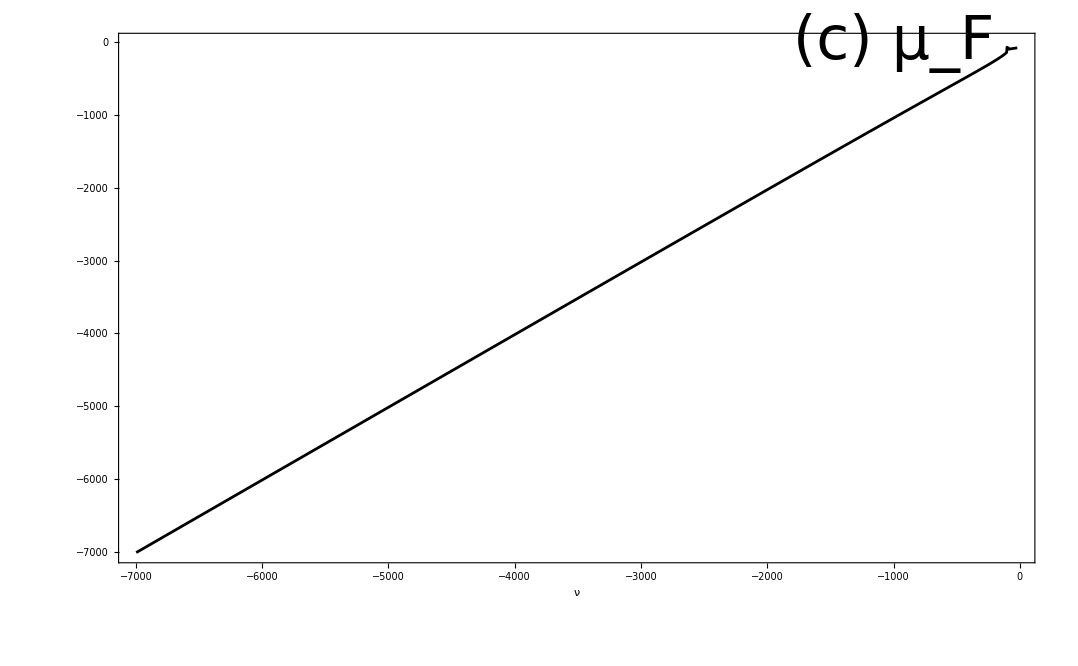

```mathematica
Data1=Table[{ν,(-FindRoot[1-(α[y,kr]-η[y,ν,kr]γ[y,kr])/β[y]*(2 σ[y]^2*(1-η[y,ν,kr])^2+ξsq[y,kr]),{y,-ν}][[1]][[2]])},{ν,-20,-7000.0,-3.0}];
p1=ListPlot[Data1,Joined->True,Axes->False,Frame->True,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2],RGBColor[0,0,0]},FrameTicksStyle->Thick];
p1label=Graphics[Text[Style["(c) μ_F",FontSize->60],{-1000,-20}]];
p100=Show[p1,p1label]
```

```mathematica
(*Fixed Point Analysis via Jacobian*)

rsq[x_,ν_,k_]:=1/β[x](α[x,k]-γ[x,k]*η[x,ν,k]);

DetMu=Data1;
DataSize=Length[DetMu];

BCoeff[x_,ν_,k_]:=-(α[x,k]-γ[x,k])^2-γ[x,k]^2* ((-3+η[x,ν,k]) (1+η[x,ν,k]))/(-1+η[x,ν,k])^2*κ[x]^2+β[x]* rsq[x,ν,k]*(3 rsq[x,ν,k] *β[x]+2 (α[x,k]-γ[x,k]));

CCoeff[x_,ν_,k_]:=γ[x,k]^4 *κ[x]^2+2 κ[x]^2* γ[x,k]^3(α[x,k]-γ[x,k]-(rsq [x,ν,k]*β[x]* (-1+2 *η[x,ν,k]))/(-1+η[x,ν,k]))+γ[x,k]^2 *κ[x]^2 ((-3+η[x,ν,k]) *(1+η[x,ν,k]))/(-1+η[x,ν,k])^2(-rsq[x,ν,k]^2 *β[x]^2+(α[x,k]-2 *rsq [x,ν,k]*β[x]-γ[x,k])^2);
Disc[x_,ν_,k_]:=1+ (4*CCoeff[x,ν,k])/BCoeff[x,ν,k]^2;

Evalsreim01=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Re,√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];
Evalsreim02=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{-√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Re,-√(-BCoeff[ef,ν,kr]/2)*(1+√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];
Evalsreim03=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Re,√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];
Evalsreim04=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{-√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Re,-√(-BCoeff[ef,ν,kr]/2)*(1-√Disc[ef,ν,kr])^(1/2)//Im},{i,1,DataSize}];

BData=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{ν,BCoeff[ef,ν,kr]},{i,1,DataSize}];
DiscData=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{ν,Disc[ef,ν,kr]},{i,1,DataSize}];
NegDiscData=Table[ν=DetMu[[i,1]];ef=Abs[DetMu[[i,2]]];{ν,-Disc[ef,ν,kr]},{i,1,DataSize}];
```

$Aborted

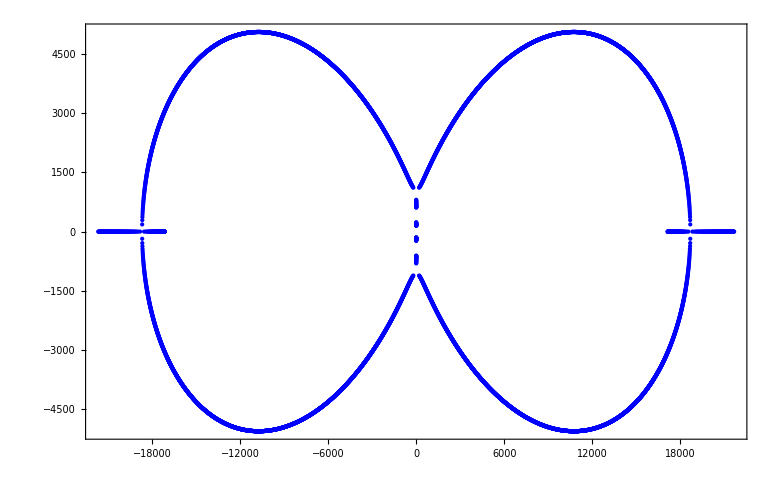

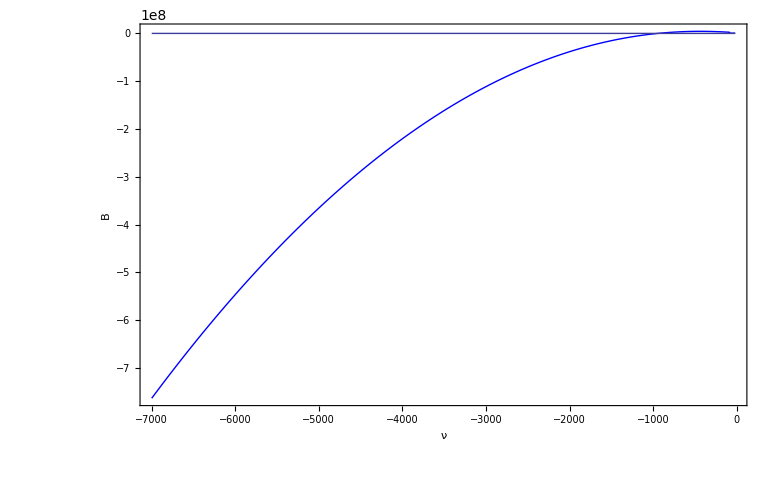

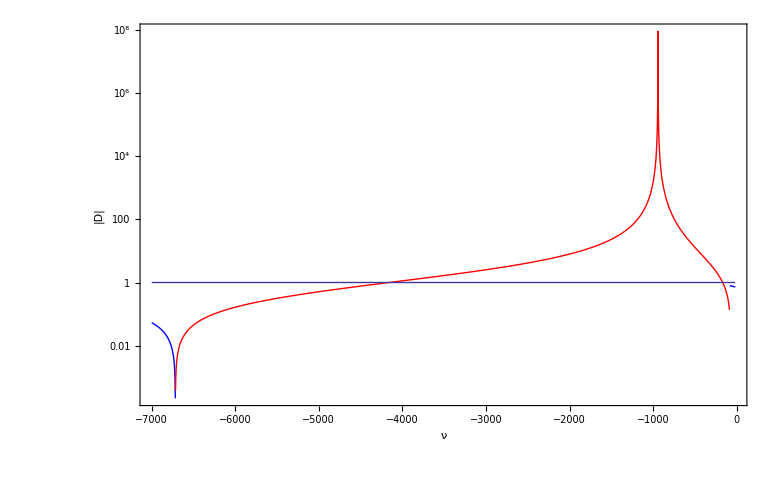

```mathematica
ListPlot[Join[Evalsreim01,Evalsreim02,Evalsreim03,Evalsreim04],Axes->True,Frame->True,FrameLabel-> {Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20},PlotStyle->{AbsoluteThickness[2],RGBColor[0,0,1]},FrameTicksStyle->Thick]

bplot=ListPlot[BData,Axes->True,Frame->True,Joined->True,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["B",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize->20]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20},PlotStyle->{AbsoluteThickness[1],RGBColor[0,0,1]},FrameTicksStyle->Thick];
zero=Plot[0,{ν,DetMu[[1,1]],DetMu[[DataSize,1]]}];
Show[bplot,zero]

logplot=ListLogPlot[{DiscData,NegDiscData},Axes->True,Frame->True,Joined->True,FrameLabel-> {Style["ν",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style[" |D| ",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20],Style["",FontFamily-> "Bitstream Vera Sans",FontSize->20]},RotateLabel->False,FrameTicksStyle->Thick,PlotRange->All,PlotStyle->{Blue,Red}];
unity=LogPlot[1,{ν,DetMu[[1,1]],DetMu[[DataSize,1]]}];
Show[logplot,unity,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]
```

```mathematica
(*Dynamics*)

ν=-140.0;(*-55.0 say*)
ϵ=FindRoot[1-(α[z,kr]-η[z,ν,kr]γ[z,kr])/β[z]*(2 σ[z]^2*(1-η[z,ν,kr])^2+ξsq[z,kr]),{z,1301}][[1]][[2]];
Print["ν = ",ν]
Print["ϵ_F = ",ϵ]
Α=α[ϵ,kr];
Print["α = ",Α]
Β=β[ϵ];
Print["β = ",Β]
Γ=γ[ϵ,kr];
Print["γ = ",Γ]
Κ=κ[ϵ];
Print["κ = ",Κ]
Λ=λ[ϵ,ν];
Print["λ = ",Λ]
```

ν = -140.

ϵ_F = 192.401

α = 33.4886

β = 1877.14

γ = 816.785

κ = 3.24535

λ = 20.4497

```mathematica
tstart=0.001;
tend=0.03;
tendnum=4000.0;
sol=NDSolve[{x'[t]+I*Γ*(x[t]-y[t])-I*Α*x[t]+I*Β*Abs[x[t]]^2*x[t]==0,y'[t]+2*I*Λ*y[t]-I*Κ*Γ*(x[t]-y[t])==0,x[0]==y[0]==gr/(√2*ϵ)},{x,y},{t,0,tendnum},MaxSteps->20000000];
ψsq[t_]:=10^2*Evaluate[Abs[y[t]]^2/.sol];
x3[t_]:=Evaluate[Re[(y[t]+y[t]*)/2.0]/.sol];
```

NDSolve::mxst: Maximum number of 20000000 steps reached at the point t == 1919.29.

$Aborted

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

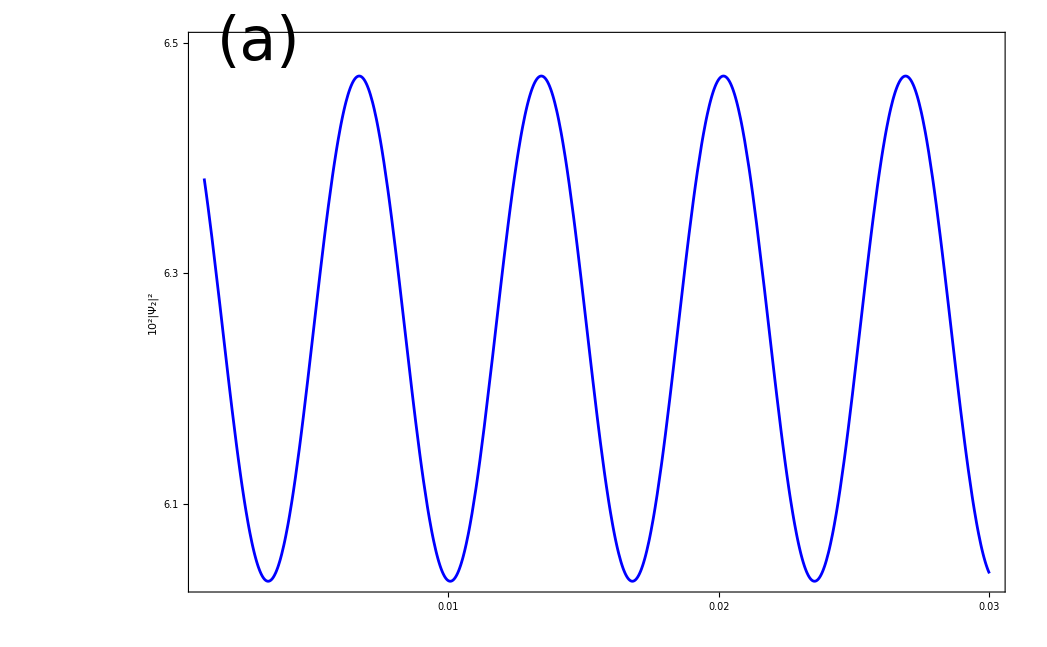

```mathematica
(*Small times*)
psq1=Plot[ψsq[t],{t,tstart,0.03},PlotRange->All,Frame->True,Axes->False,FrameLabel-> {Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},FrameTicks-> {{{6.1,6.3,6.5},None},{{0.01,0.02,0.03},None}},FrameTicksStyle->Thickness[0.01]];
psq1label=Graphics[Text[Style["(a)",FontSize->60],{0.003,6.5}]];
Show[psq1,psq1label]
```

```mathematica
(*Average out the small oscillations*)
t1=0.007;
t2=0.0134;
tpm=t2-t1;
Subscript[Ω, m]=(2π)/tpm;(*Small oscillation frequency*)

Print["Small Oscillation Frequency Ω_m = ",Subscript[Ω, m]]
```

Small Oscillation Frequency Ω_m = 981.748

Small Oscillation Frequency Ω_m = 1079.59

Small Oscillation Frequency Ω_m = 1079.59

Small Oscillation Frequency Ω = 1079.59

Small Oscillation Frequency Ω = 3488.72

Small Oscillation Frequency Ω = (2 π)/tp

Small Oscillation Frequency Ω = 1401.56

Small Oscillation Frequency Ω = 1401.56

Small Oscillation Frequency Ω = 1401.56

«3 more identical outputs»

Small Oscillation Frequency Ω = 3488.72

Small Oscillation Frequency Ω = 3488.72

Small Oscillation Frequency Ω = 1388.55

Small Oscillation Frequency Ω = 1388.55

Small Oscillation Frequency Ω = 1388.55

Small Oscillation Frequency Ω = 3477.14

Small Oscillation Frequency Ω = 1396.26

Small Oscillation Frequency Ω = 1392.24

Small Oscillation Frequency Ω = 1392.24

Small Oscillation Frequency Ω = 1395.33

Small Oscillation Frequency Ω = 1408.47

Small Oscillation Frequency Ω = 1392.24

Small Oscillation Frequency Ω = 1395.33

Small Oscillation Frequency Ω = 3514.09

Small Oscillation Frequency Ω = 3514.09

Small Oscillation Frequency Ω = 3514.09
Small Oscillation Frequency Ω = 3514.09

Small Oscillation Frequency Ω = 1408.47
(*Small Oscillation Frequency Ω = 1408.47*)

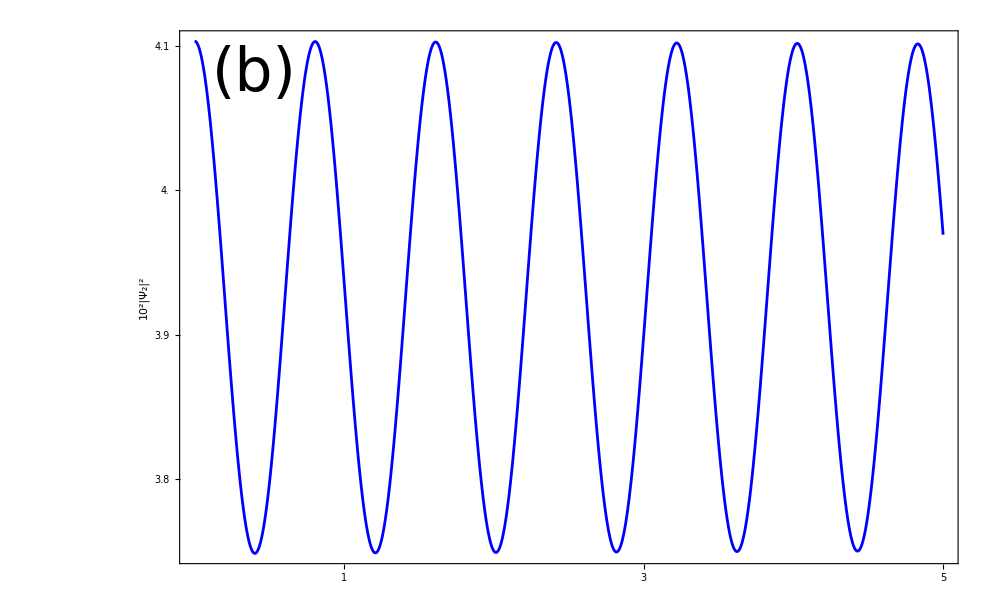

```mathematica
Envelope=Table[{t,ψsq[t][[1]]},{t,0,5.0,tpm}];
EnvPlot=ListPlot[Envelope,Joined->True,
PlotRange->All,Frame->True,Axes->False,FrameLabel-> {Style[" ",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},FrameTicks->{{{6.1,6.3,6.5},None},{{0.01,0.02,0.03},None}},FrameTicksStyle->Thickness[0.01]];
EnvLabel=Graphics[Text[Style["(b)",FontSize->60],{0.4,6.5}]];
Show[EnvPlot,EnvLabel]
```

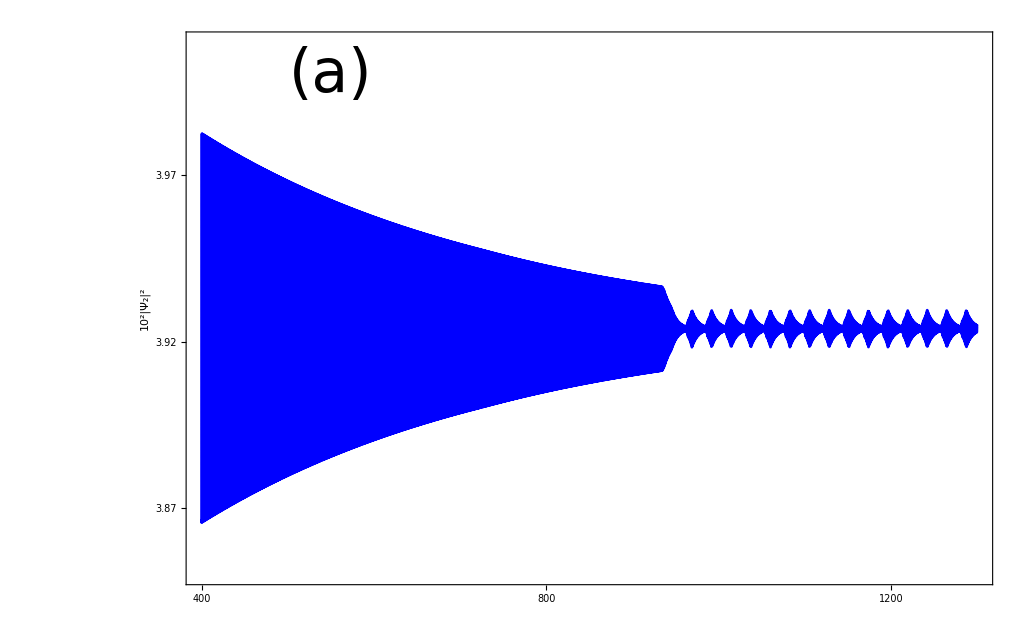

Larger Oscillation Frequency Ω = 10.324

Larger Oscillation Frequency Ω = 10.1834

```mathematica
(*SO THERE IS ANOTHER OSCILLATION!!!!!*)
(*Keep plotting it*)


Envelope=Table[{t,ψsq[t][[1]]},{t,400,1300.0,tpm}];
EnvPlot=ListPlot[Envelope,Joined->True,PlotRange->{3.85,4.01},Frame->True,Axes->False,FrameLabel-> {Style["",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},
FrameTicks-> {{{3.87,3.92,3.97},None},{{400,800,1200},None}},FrameTicksStyle->Thickness[0.01]];
EnvLabel=Graphics[Text[Style["(a)",FontSize->60],{550,4.0}]];
Show[EnvPlot,EnvLabel]
```

```mathematica
FinalPlot=Plot[ψsq[t][[1]],{t,130,170},PlotRange->{2.115,2.145},Frame->True,Axes->False,FrameLabel-> {Style["t",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["10^2|Ψ_2|^2",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},
FrameTicks-> {{{2.12,2.13,2.14},None},{{130,145,160},None}},FrameTicksStyle->Thickness[0.01](*,PlotPoints-> 250*)];
FinalLabel=Graphics[Text[Style["(h)",FontSize->60],{135,2.143}]];
Show[FinalPlot,FinalLabel]
```

```mathematica
(*Calculation of relaxation and revival times*)
ψmax=2.138;
ψmin=2.120;
ψavg=(ψmax+ψmin)/2.0;
ψdif=(ψmax-ψmin)/2.0;
ψrelax=ψdif/2.7818281828459045235;
ψatrelax=ψrelax+ψavg;
Print["Amplitude at t_r=",ψatrelax]
tR=147.1-144.7;
Print["Revival time t_R=",tR]
trelaxbegin=136.2;
trelaxend=140.5;
Print["Relaxation time t_r=",trelaxend-trelaxbegin]
```

Amplitude at t_r=2.13224

Revival time t_R=2.4

Relaxation time t_r=4.3

```mathematica
(*Plot of Subscript[Ω, b0]*)

AFirst[ϵ_,k_,ν_]:=γ[ϵ,k]-α[ϵ,k]+2*λ[ϵ,ν]-κ[ϵ]*γ[ϵ,k];
BSecond[ϵ_,k_,ν_]:=(γ[ϵ,k]-α[ϵ,k])(2*λ[ϵ,ν]+κ[ϵ]*γ[ϵ,k])-κ[ϵ]*γ[ϵ,k]^2;
Freq[ϵ_,k_,ν_]:=AFirst[ϵ,k,ν]*√(1-4*BSecond[ϵ,k,ν]/AFirst[ϵ,k,ν]^2);
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

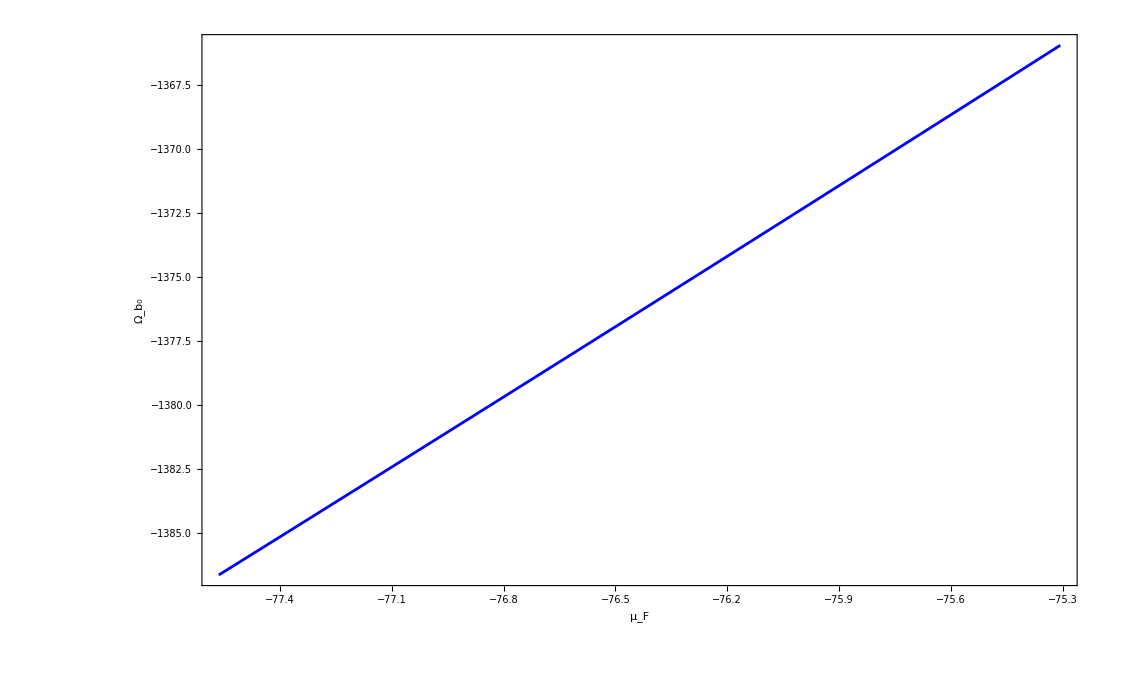

```mathematica
νinit=-10.0;
νfinal=-0.1;
νincr=0.01;
FreqList=Table[ν,{ν,νinit, νfinal,νincr}];
Bose1=Fermi1;
L=Length[FreqList]+1;
For[i=1,i≤ L-1,i++,
ν=νinit+i*νincr;
e=FindRoot[1-(α[e,kr]-η[e,ν,kr]γ[e,kr])/β[e]*(2 σ[e]^2*(1-η[e,ν,kr])^2+ξsq[e,kr]),{e,1301}][[1]][[2]];
FreqList[[i]]= {-e,Freq[e,kr,ν]};

];
FreqPlot=ListPlot[FreqList,Joined->True,Frame->True,Axes->False,FrameLabel-> {Style["μ_F ",FontFamily-> "Bitstream Vera Sans",FontSize-> 50],Style["Ω_b_0",FontFamily-> "Bitstream Vera Sans",FontSize->50]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 50},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},FrameTicksStyle->Thickness[0.01]]
```

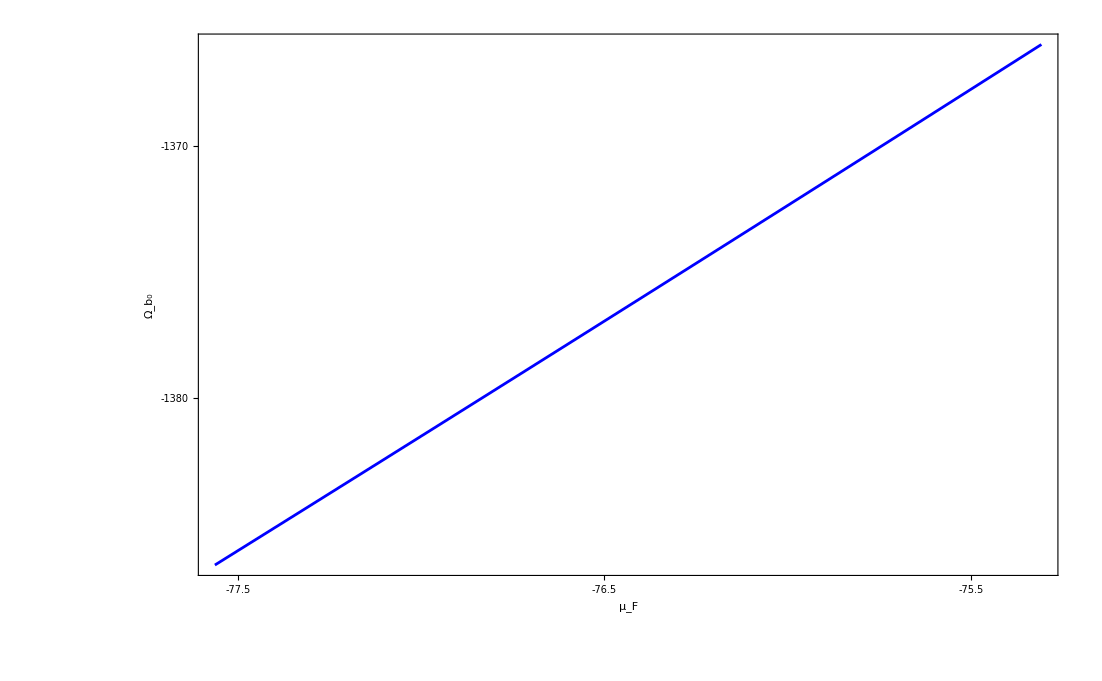

```mathematica
Show[%,FrameTicks-> {{{-1380,-1370},None},{{-77.5,-76.5,-75.5},None}}]
```

```mathematica
(*Plot x3[t] = Real part of Subscript[Ψ, 2]*)
Plot[x3[t],{t,0,10},Frame->True,Axes->False]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

-Graphics-

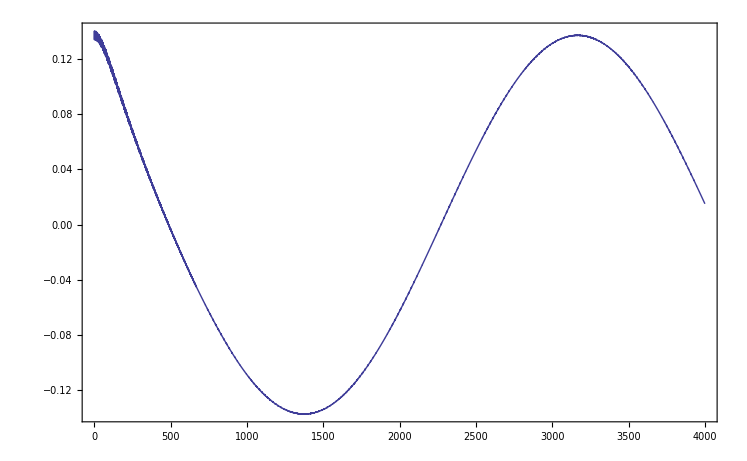

```mathematica
(*From above, time period is 0.544*)
(*Now, factor out this signal*)
tdel=0.544;

bigx3data=Table[{t,x3[t][[1]]},{t,0.0,4000,tdel}];
ListPlot[bigx3data,Joined->True,Frame->True,Axes->False,FrameLabel-> {Style["t",FontFamily-> "Bitstream Vera Sans",FontSize-> 20],Style["x_3(t)",FontFamily-> "Bitstream Vera Sans",FontSize->20]},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20},PlotStyle->{AbsoluteThickness[2], RGBColor[0,0,1]},FrameTicksStyle->Thickness[0.01]]
```

```mathematica
FactorInteger[{587435,388716}]
```

{{{5,1},{17,1},{6911,1}},{{2,2},{3,1},{29,1},{1117,1}}}